## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.02,0.016 ,0.014,0.012,0.011,0.01,0.0093, 0.008 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,0.00930000,0.00800000}

```mathematica
wtlist={0.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,3}],{idx,0,2}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.7500_T",Tstring[[13]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,3}],{idx,0,2}];
```

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime0.00_idx0.nc.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime0.00_idx0.nc is not a valid file, directory, or URL specification.

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime80000.00_idx0.nc.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime80000.00_idx0.nc is not a valid file, directory, or URL specification.

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime90000.00_idx0.nc.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/overlapCRoverlap_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime90000.00_idx0.nc is not a valid file, directory, or URL specification.

General::stop: Further output of Import::chtype will be suppressed during this calculation.

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.7500_T",Tstring[[13]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,3}];
```

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime0.00_idx1.nc.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime0.00_idx1.nc is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦4,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime80000.00_idx1.nc.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime80000.00_idx1.nc is not a valid file, directory, or URL specification.

Part::partw: Part 13 of {0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime90000.00_idx1.nc.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Import::chtype: First argument /home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/glassyDynamics_N4096_p3.7500_T<>{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,«2»}⟦13⟧<>_waitingTime90000.00_idx1.nc is not a valid file, directory, or URL specification.

General::stop: Further output of Import::chtype will be suppressed during this calculation.

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,3}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->All]
```

-Graphics-

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,3}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[3],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->{All,{0,1}}]
```

Part::partd: Part specification {{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed}}⟦1,1,2,1⟧ is longer than depth of object.

Part::partd: Part specification {{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed}}⟦2,1,2,1⟧ is longer than depth of object.

Part::partd: Part specification {{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed},{$Failed,$Failed,$Failed}}⟦3,1,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.7500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Table[Length[overlap[[T,2,1]]],{T,Length[Tlist]}]
```

{91,91,94,99,111,108,129,131,131,118,131,123}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.7500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtlistLongestString[[7]],"_idx0.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}];
```

```mathematica
Length[time]
```

131

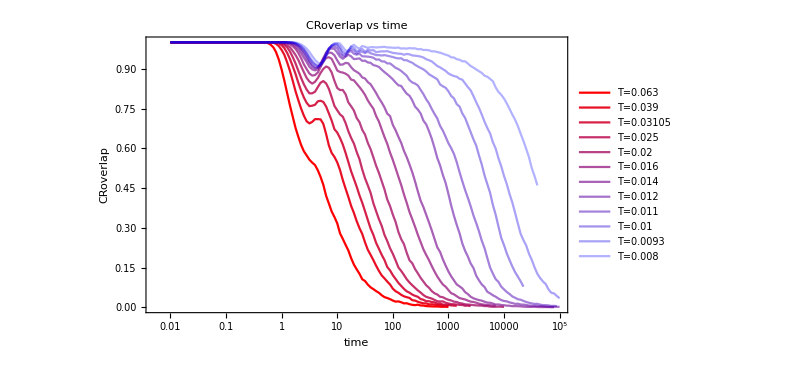

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={5.852982645345412,12.037225643329087,15.821965290011322,20.80060772081055,28.433194549659632,33.29863650395622,42.913661721841,52.20821748835159,46.47967018518446,51.24062795780368,63.48723142372112,64.75414980350477};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{47,53,55,58,61,62,64,66,65,66,68,68}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.98997 ⅇ^(-0.308609 t^0.575583)],FittedModel[0.989982 ⅇ^(-0.168593 t^0.601921)],FittedModel[0.989989 ⅇ^(-0.109138 t^0.639612)],FittedModel[0.989992 ⅇ^(-0.0735061 t^0.660383)],FittedModel[0.989994 ⅇ^(-0.0421592 t^0.689391)],FittedModel[0.989998 ⅇ^(-0.018869 t^0.740439)],FittedModel[0.989997 ⅇ^(-0.0124505 t^0.734414)],FittedModel[0.97732 ⅇ^(-0.00252679 t^0.8356)],FittedModel[0.984432 ⅇ^(-0.00214424 t^0.777919)],FittedModel[0.962506 ⅇ^(-0.000314139 t^0.908698)],FittedModel[0.980311 ⅇ^(-0.000305001 t^0.833892)],FittedModel[0.982221 ⅇ^(-0.000076728 t^0.866982)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{7.71055,19.2525,31.921,52.083,98.7804,213.15,392.328,1283.69,2695.24,7158.64,16444.3,55770.5}

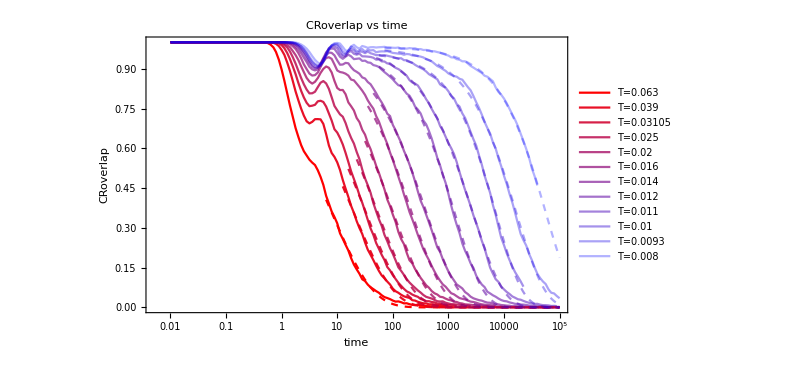

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

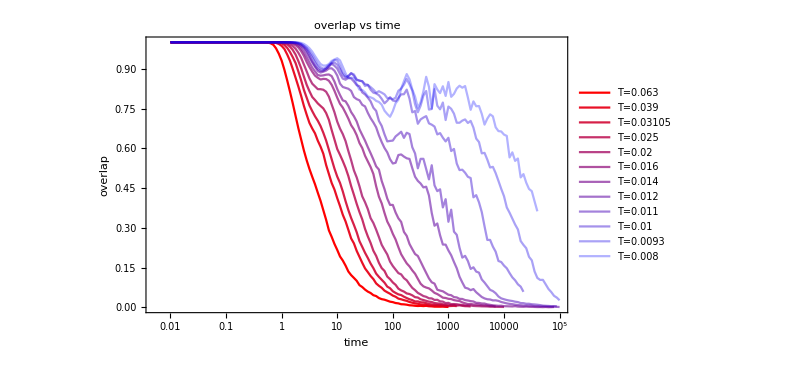

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
fitOverlapStartNum={5.271207498726352,9.075387311350442,11.234708221147047,14.180299161903513,14.458137795823296,18.97098530539023,22.156727577851406,245.72505344710865,316.2277660168386,466.1646378111317,834.3500851569818,1013.0199016364572};
```

```mathematica
fitOverlapStartPos=Table[Position[time,_?(#>fitOverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{46,51,53,55,55,57,58,79,81,85,90,92}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.9>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.899971 ⅇ^(-0.37639 t^0.563525)],FittedModel[0.899981 ⅇ^(-0.209361 t^0.606347)],FittedModel[0.899985 ⅇ^(-0.172763 t^0.606202)],FittedModel[0.899991 ⅇ^(-0.109131 t^0.660386)],FittedModel[0.899996 ⅇ^(-0.0885876 t^0.636126)],FittedModel[0.899998 ⅇ^(-0.0413426 t^0.710072)],FittedModel[0.899998 ⅇ^(-0.0437745 t^0.635467)],FittedModel[0.89998 ⅇ^(-0.0149191 t^0.660698)],FittedModel[0.89999 ⅇ^(-0.013667 t^0.613477)],FittedModel[0.87357 ⅇ^(-0.00325518 t^0.679926)],FittedModel[0.855909 ⅇ^(-0.000849259 t^0.729594)],FittedModel[0.8867 ⅇ^(-0.000529233 t^0.699028)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{5.66302,13.1823,18.1097,28.6288,45.1591,88.8258,137.48,580.94,1093.83,4553.8,16185.9,48641.9}

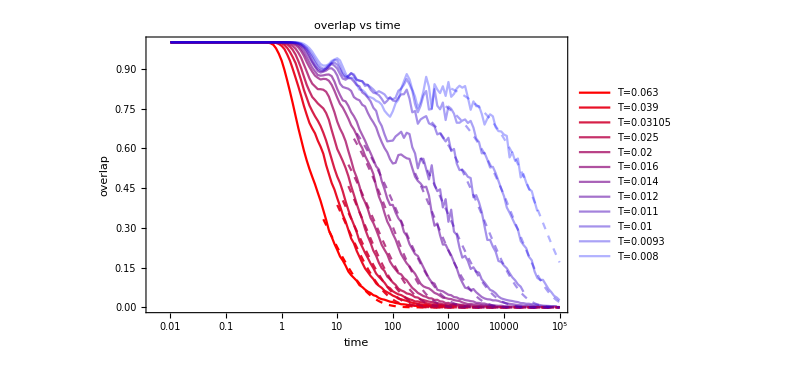

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

Show::gcomb: Could not combine the graphics objects in Show[CRoverlapfitST,CRoverlapLTPlot,{}].

#### CRSISF

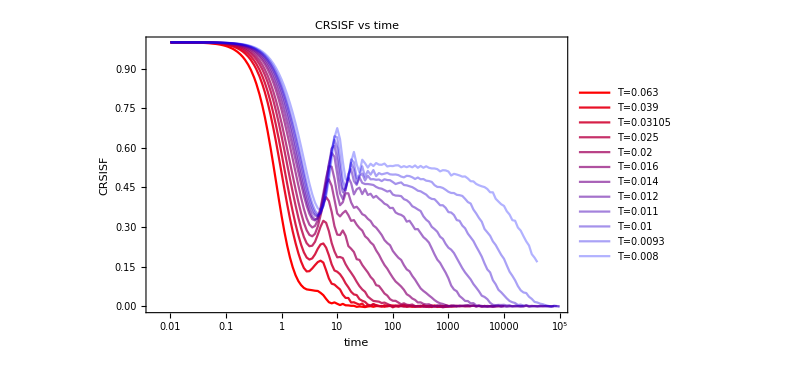

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={6.421020423262568,10.650828740730146,12.458832828182784,14.576026130799443,19.924443715687687,26.237572659796527,28.976232281437134,37.38913876160977,47.243690497792436,59.69091806663826,63.323102094246536,67.20778364461461};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{48,52,53,55,57,60,61,63,65,67,68,68}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.0844453 ⅇ^(-0.297464 t^0.889328)],FittedModel[0.595275 ⅇ^(-0.281234 t^0.870389)],FittedModel[0.586445 ⅇ^(-0.206324 t^0.839256)],FittedModel[0.598356 ⅇ^(-0.167595 t^0.776503)],FittedModel[0.430533 ⅇ^(-0.0641531 t^0.826335)],FittedModel[0.491829 ⅇ^(-0.0384996 t^0.792872)],FittedModel[0.470951 ⅇ^(-0.0233685 t^0.763431)],FittedModel[0.449396 ⅇ^(-0.00286934 t^0.899984)],FittedModel[0.481917 ⅇ^(-0.00296103 t^0.804773)],FittedModel[0.485637 ⅇ^(-0.000573669 t^0.899982)],FittedModel[0.506188 ⅇ^(-0.000268545 t^0.899972)],FittedModel[0.535728 ⅇ^(-0.000138403 t^0.853029)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.90925,4.2951,6.55747,9.97736,27.7627,60.8242,137.053,667.94,1386.6,3995.4,9287.15,33397.2}

```mathematica
Length[TlistLongest]
```

0

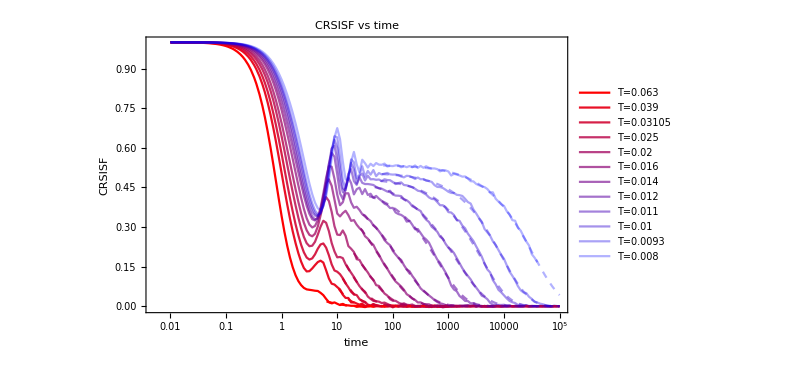

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

#### SISF

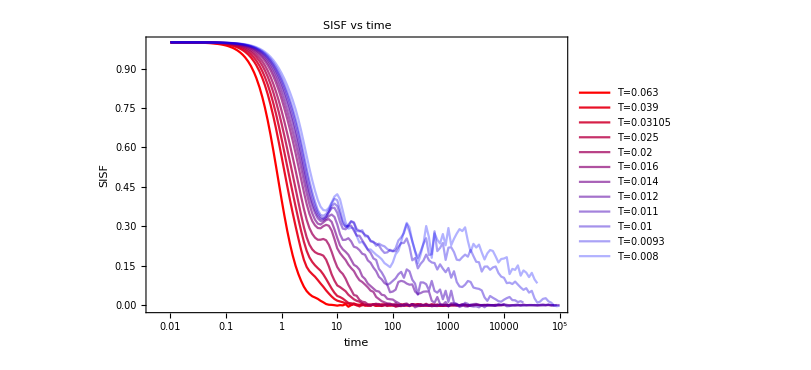

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
time[[54]]
```

14.13

```mathematica
fitSISFStartPos={45,50,50,52,54,59,59,75,75,85,85,85}
```

{45,50,50,52,54,59,59,75,75,85,85,85}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.494605 ⅇ^(-0.832851 t^0.897997)],FittedModel[0.343289 ⅇ^(-0.564287 t^0.718438)],FittedModel[0.424179 ⅇ^(-0.308476 t^0.896053)],FittedModel[0.399815 ⅇ^(-0.194805 t^0.898468)],FittedModel[0.499887 ⅇ^(-0.160107 t^0.899911)],FittedModel[0.359975 ⅇ^(-0.0699671 t^0.899451)],FittedModel[0.498041 ⅇ^(-0.154475 t^0.677195)],FittedModel[0.171919 ⅇ^(-0.00697936 t^0.898628)],FittedModel[0.160174 ⅇ^(-0.00353881 t^0.899578)],FittedModel[0.499375 ⅇ^(-0.118738 t^0.358919)],FittedModel[0.250492 ⅇ^(-0.00181472 t^0.668758)],FittedModel[0.279521 ⅇ^(-0.00103854 t^0.66663)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{1.2259,2.21763,3.71562,6.1756,7.65732,19.2413,15.7688,250.853,530.602,378.721,12558.3,29896.3}

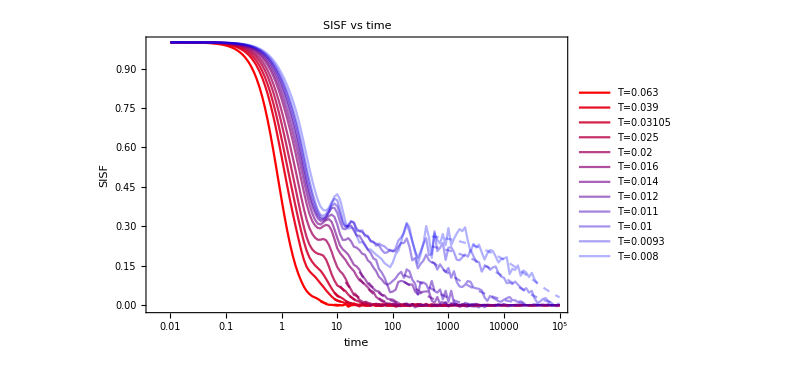

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

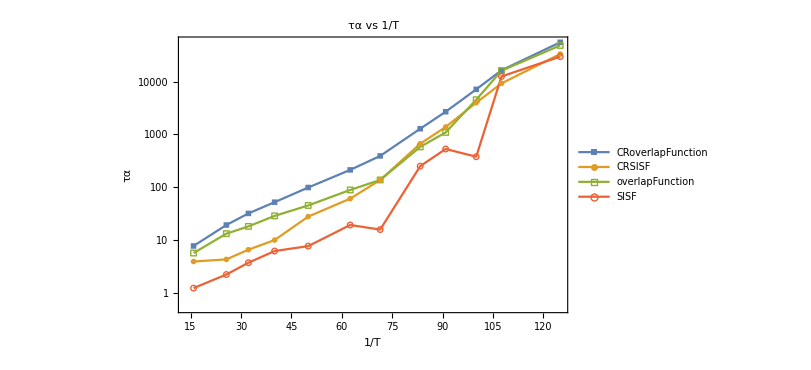

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCRSISFfits[[T]],tauCROverlapfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,3.90925,7.71055,5.66302,1.2259},{0.039,4.2951,19.2525,13.1823,2.21763},{0.03105,6.55747,31.921,18.1097,3.71562},{0.025,9.97736,52.083,28.6288,6.1756},{0.02,27.7627,98.7804,45.1591,7.65732},{0.016,60.8242,213.15,88.8258,19.2413},{0.014,137.053,392.328,137.48,15.7688},{0.012,667.94,1283.69,580.94,250.853},{0.011,1386.6,2695.24,1093.83,530.602},{0.01,3995.4,7158.64,4553.8,378.721},{0.0093,9287.15,16444.3,16185.9,12558.3},{0.008,33397.2,55770.5,48641.9,29896.3}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP375.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP375.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p375.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

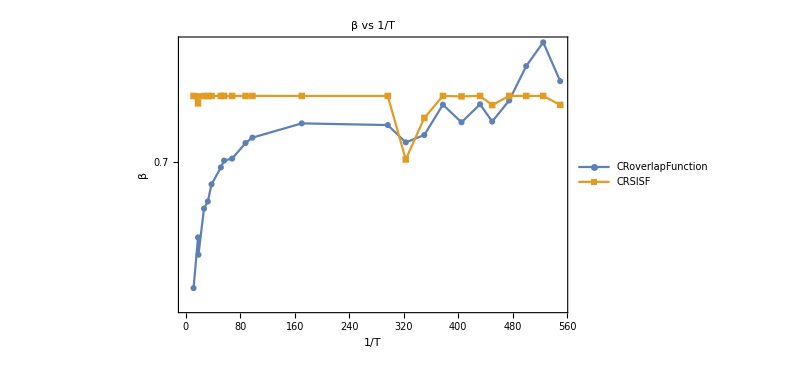

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

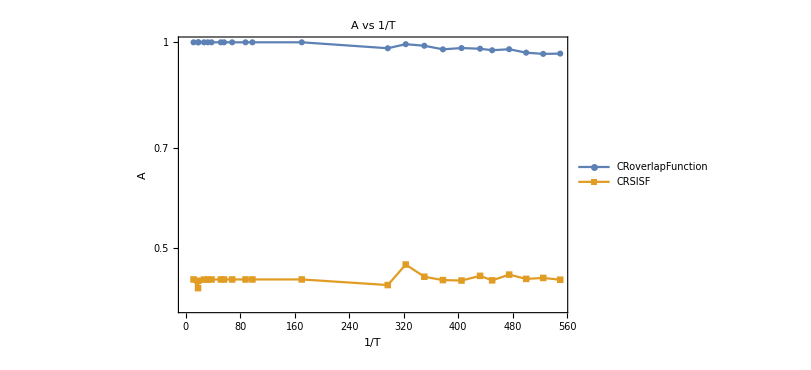

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

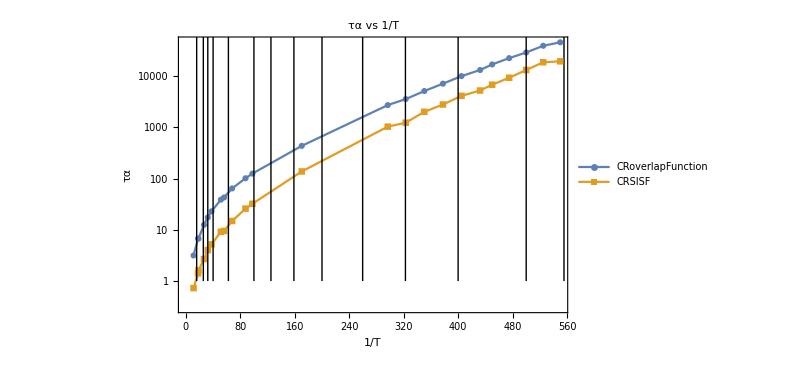

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

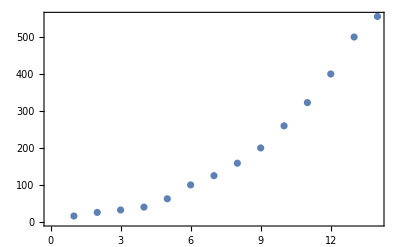

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16